# Examen parcial III sistemas dinámicos no lineales, 2024/2, parte práctica (matutino)

## Pregunta I

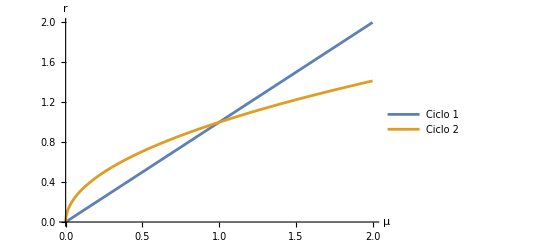

```mathematica
Plot[{m,Sqrt[m]},{m,0,2},AxesLabel->{μ,r},PlotLegends->{"Ciclo 1","Ciclo 2"}]
```

```mathematica
Evaluate@TransformedField["Polar"->"Cartesian",{r*(-1-r)*(-1-r^2),-1},{r,θ}->{x[t],y[t]}]
```

{y[t]/(√(x[t]^2+y[t]^2))+x[t] (-1-x[t]^2-y[t]^2) (-1-√(x[t]^2+y[t]^2)),-x[t]/(√(x[t]^2+y[t]^2))+y[t] (-1-x[t]^2-y[t]^2) (-1-√(x[t]^2+y[t]^2))}

```mathematica
csol1=NDSolve[{x'[t]==y[t]/(√(x[t]^2+y[t]^2))+x[t] (-1-x[t]^2-y[t]^2) (-1-√(x[t]^2+y[t]^2)),y'[t]==-x[t]/(√(x[t]^2+y[t]^2))+y[t] (-1-x[t]^2-y[t]^2) (-1-√(x[t]^2+y[t]^2)),x[0]==0.001,y[0]==0},{x,y},{t,0,6}];
```

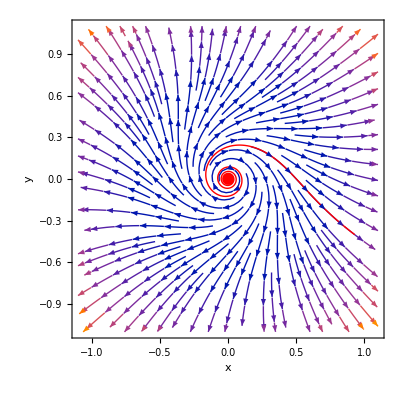

```mathematica
Show[{StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(-1-r)*(-1-r^2),-1},{r,θ}->{x,y}],{x,-1.1,1.1},{y,-1.1,1.1},FrameLabel->{x,y}],ParametricPlot[Evaluate[{x[t],y[t]}/.csol1],{t,0,6},PlotStyle->{Red,Thick},PlotRange->{{-1.1,1.1},{-1.1,1.1}}]}]
```

```mathematica
Evaluate@TransformedField["Polar"->"Cartesian",{r*(-r)*(-r^2),-1},{r,θ}->{x[t],y[t]}]
```

{y[t]/(√(x[t]^2+y[t]^2))+x[t] (x[t]^2+y[t]^2)^(3/2),-x[t]/(√(x[t]^2+y[t]^2))+y[t] (x[t]^2+y[t]^2)^(3/2)}

```mathematica
csol2=NDSolve[{x'[t]==y[t]/(√(x[t]^2+y[t]^2))+x[t] (x[t]^2+y[t]^2)^(3/2),y'[t]==-x[t]/(√(x[t]^2+y[t]^2))+y[t] (x[t]^2+y[t]^2)^(3/2),x[0]==0.1,y[0]==0},{x,y},{t,0,400}];
```

NDSolve::ndsz: At t == 333.219, step size is effectively zero; singularity or stiff system suspected.

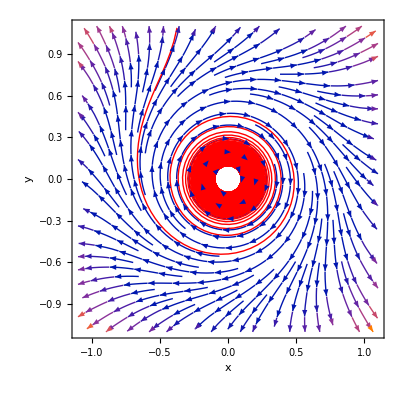

```mathematica
Show[{StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(-r)*(-r^2),-1},{r,θ}->{x,y}],{x,-1.1,1.1},{y,-1.1,1.1},FrameLabel->{x,y}],ParametricPlot[Evaluate[{x[t],y[t]}/.csol2],{t,0,333},PlotStyle->{Red,Thick},PlotRange->{{-1.1,1.1},{-1.1,1.1}},PlotPoints->100]}]
```

```mathematica
Evaluate@TransformedField["Polar"->"Cartesian",{r*(1/5-r)*(1/5-r^2),-1},{r,θ}->{x[t],y[t]}]
```

{y[t]/(√(x[t]^2+y[t]^2))+x[t] (1/5-x[t]^2-y[t]^2) (1/5-√(x[t]^2+y[t]^2)),-x[t]/(√(x[t]^2+y[t]^2))+y[t] (1/5-x[t]^2-y[t]^2) (1/5-√(x[t]^2+y[t]^2))}

```mathematica
csol3=NDSolve[{x'[t]==y[t]/(√(x[t]^2+y[t]^2))+x[t] (1/5-x[t]^2-y[t]^2) (1/5-√(x[t]^2+y[t]^2)),y'[t]==-x[t]/(√(x[t]^2+y[t]^2))+y[t] (1/5-x[t]^2-y[t]^2) (1/5-√(x[t]^2+y[t]^2)),x[0]==0.01,y[0]==0},{x,y},{t,0,100}];
csol4=NDSolve[{x'[t]==y[t]/(√(x[t]^2+y[t]^2))+x[t] (1/5-x[t]^2-y[t]^2) (1/5-√(x[t]^2+y[t]^2)),y'[t]==-x[t]/(√(x[t]^2+y[t]^2))+y[t] (1/5-x[t]^2-y[t]^2) (1/5-√(x[t]^2+y[t]^2)),x[0]==0.45,y[0]==0},{x,y},{t,0,50}];
```

NDSolve::ndsz: At t == 35.7148, step size is effectively zero; singularity or stiff system suspected.

```mathematica
csol5=NDSolve[{x'[t]==y[t]/(√(x[t]^2+y[t]^2))+x[t] (1/5-x[t]^2-y[t]^2) (1/5-√(x[t]^2+y[t]^2)),y'[t]==-x[t]/(√(x[t]^2+y[t]^2))+y[t] (1/5-x[t]^2-y[t]^2) (1/5-√(x[t]^2+y[t]^2)),x[0]==0.3,y[0]==0},{x,y},{t,0,100}];
```

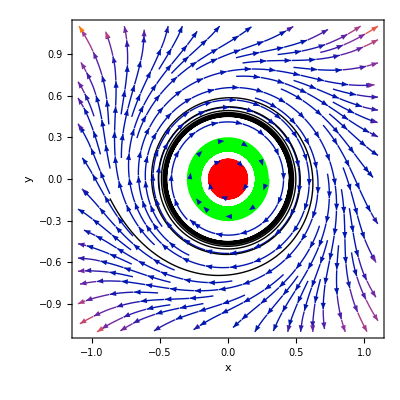

```mathematica
Show[{StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1/5-r)*(1/5-r^2),-1},{r,θ}->{x,y}],{x,-1.1,1.1},{y,-1.1,1.1},FrameLabel->{x,y}],ParametricPlot[Evaluate[{x[t],y[t]}/.csol3],{t,0,100},PlotStyle->{Red,Thick},PlotRange->{{-1.1,1.1},{-1.1,1.1}}],ParametricPlot[Evaluate[{x[t],y[t]}/.csol5],{t,0,100},PlotStyle->{Green,Thick},PlotRange->{{-1.1,1.1},{-1.1,1.1}}],ParametricPlot[Evaluate[{x[t],y[t]}/.csol4],{t,0,35},PlotStyle->{Black,Thick},PlotRange->{{-1.1,1.1},{-1.1,1.1}}]}]
```

```mathematica
Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r)*(1-r^2),-1},{r,θ}->{x[t],y[t]}]
```

{y[t]/(√(x[t]^2+y[t]^2))+x[t] (1-x[t]^2-y[t]^2) (1-√(x[t]^2+y[t]^2)),-x[t]/(√(x[t]^2+y[t]^2))+y[t] (1-x[t]^2-y[t]^2) (1-√(x[t]^2+y[t]^2))}

```mathematica
csol6=NDSolve[{x'[t]==y[t]/(√(x[t]^2+y[t]^2))+x[t] (1-x[t]^2-y[t]^2) (1-√(x[t]^2+y[t]^2)),y'[t]==-x[t]/(√(x[t]^2+y[t]^2))+y[t] (1-x[t]^2-y[t]^2) (1-√(x[t]^2+y[t]^2)),x[0]==0.01,y[0]==0},{x,y},{t,0,100}];
csol7=NDSolve[{x'[t]==y[t]/(√(x[t]^2+y[t]^2))+x[t] (1-x[t]^2-y[t]^2) (1-√(x[t]^2+y[t]^2)),y'[t]==-x[t]/(√(x[t]^2+y[t]^2))+y[t] (1-x[t]^2-y[t]^2) (1-√(x[t]^2+y[t]^2)),x[0]==1.01,y[0]==0},{x,y},{t,0,46}];
```

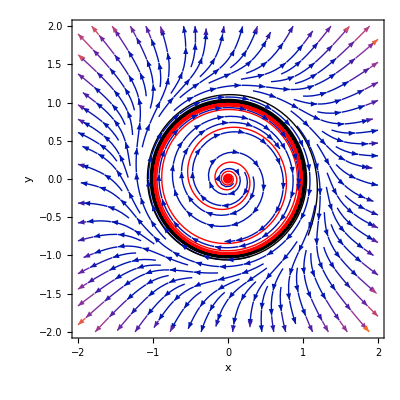

```mathematica
Show[{StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r)*(1-r^2),-1},{r,θ}->{x,y}],{x,-2,2},{y,-2,2},FrameLabel->{x,y}],ParametricPlot[Evaluate[{x[t],y[t]}/.csol6],{t,0,100},PlotStyle->{Red,Thick},PlotRange->{{-1.1,1.1},{-1.1,1.1}}],ParametricPlot[Evaluate[{x[t],y[t]}/.csol7],{t,0,46},PlotStyle->{Black,Thick},PlotRange->{{-1.1,1.1},{-1.1,1.1}}]}]
```

```mathematica
Evaluate@TransformedField["Polar"->"Cartesian",{r*(2-r)*(2-r^2),-1},{r,θ}->{x[t],y[t]}]
```

{y[t]/(√(x[t]^2+y[t]^2))+x[t] (2-x[t]^2-y[t]^2) (2-√(x[t]^2+y[t]^2)),-x[t]/(√(x[t]^2+y[t]^2))+y[t] (2-x[t]^2-y[t]^2) (2-√(x[t]^2+y[t]^2))}

```mathematica
csol8=NDSolve[{x'[t]==y[t]/(√(x[t]^2+y[t]^2))+x[t] (2-x[t]^2-y[t]^2) (2-√(x[t]^2+y[t]^2)),y'[t]==-x[t]/(√(x[t]^2+y[t]^2))+y[t] (2-x[t]^2-y[t]^2) (2-√(x[t]^2+y[t]^2)),x[0]==0.01,y[0]==0},{x,y},{t,0,100}];
csol9=NDSolve[{x'[t]==y[t]/(√(x[t]^2+y[t]^2))+x[t] (2-x[t]^2-y[t]^2) (2-√(x[t]^2+y[t]^2)),y'[t]==-x[t]/(√(x[t]^2+y[t]^2))+y[t] (2-x[t]^2-y[t]^2) (2-√(x[t]^2+y[t]^2)),x[0]==1.99,y[0]==0},{x,y},{t,0,100}];
csol10=NDSolve[{x'[t]==y[t]/(√(x[t]^2+y[t]^2))+x[t] (2-x[t]^2-y[t]^2) (2-√(x[t]^2+y[t]^2)),y'[t]==-x[t]/(√(x[t]^2+y[t]^2))+y[t] (2-x[t]^2-y[t]^2) (2-√(x[t]^2+y[t]^2)),x[0]==2.01,y[0]==0},{x,y},{t,0,50}];
```

NDSolve::ndsz: At t == 0.845869, step size is effectively zero; singularity or stiff system suspected.

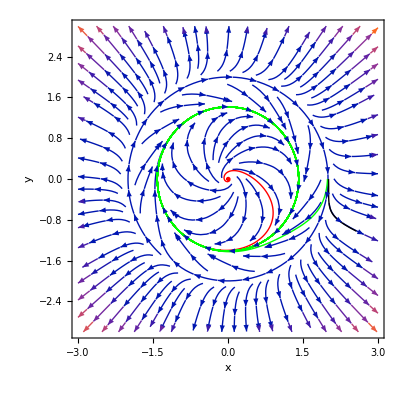

```mathematica
Show[{StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(2-r)*(2-r^2),-1},{r,θ}->{x,y}],{x,-3,3},{y,-3,3},FrameLabel->{x,y}],ParametricPlot[Evaluate[{x[t],y[t]}/.csol8],{t,0,100},PlotStyle->{Red,Thick},PlotRange->{{-1.1,1.1},{-1.1,1.1}}],ParametricPlot[Evaluate[{x[t],y[t]}/.csol9],{t,0,100},PlotStyle->{Green,Thick},PlotRange->{{-1.1,1.1},{-1.1,1.1}}],ParametricPlot[Evaluate[{x[t],y[t]}/.csol10],{t,0,0.8},PlotStyle->{Black,Thick},PlotRange->{{-1.1,1.1},{-1.1,1.1}}]}]
```

Diagrama de bifurcación

```mathematica
Show[{ContourPlot3D[Sqrt[x^2+y^2]==m,{m,-1/2,2},{x,-3,3},{y,-3,3},Mesh->None,ContourStyle->Directive[Blue,Opacity[0.4],Specularity[White,30]],AxesLabel->{μ,x,y}],ContourPlot3D[Sqrt[x^2+y^2]==Sqrt[m],{m,-1/2,2},{x,-3,3},{y,-3,3},Mesh->None,ContourStyle->Directive[Red,Opacity[0.4],Specularity[White,30]]],ParametricPlot3D[{m,0,0},{m,-1/2,2},PlotStyle->{Thick,Dashed,Black}]}]
```

-Graphics3D-

## Pregunta II

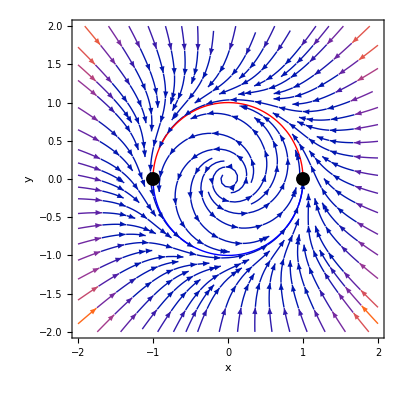

```mathematica
sol1=NDSolve[{r'[t]==r[t]*(1-r[t]^2)*(r[t]^2*Sin[v[t]]^2+(r[t]^2*Cos[v[t]]^2-1)^2),v'[t]==r[t]^2*Sin[v[t]]^2+(r[t]^2*Cos[v[t]]^2-1)^2,r[500]==1,v[500]==Pi/2},{r,v},{t,0,1000}];
sol2=NDSolve[{r'[t]==r[t]*(1-r[t]^2)*(r[t]^2*Sin[v[t]]^2+(r[t]^2*Cos[v[t]]^2-1)^2),v'[t]==r[t]^2*Sin[v[t]]^2+(r[t]^2*Cos[v[t]]^2-1)^2,r[500]==1,v[500]==3*Pi/2},{r,v},{t,0,1000}];
Show[{StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2)*(r^2*Sin[θ]^2+(r^2*Cos[θ]^2-1)^2),r^2*Sin[θ]^2+(r^2*Cos[θ]^2-1)^2},{r,θ}->{x,y}],{x,-2,2},{y,-2,2},FrameLabel->{x,y}],ParametricPlot[Evaluate[{r[t]*Cos[v[t]],r[t]*Sin[v[t]]}/.sol1],{t,0,1000},PlotStyle->{Red,Thick},PlotPoints->500],ParametricPlot[Evaluate[{r[t]*Cos[v[t]],r[t]*Sin[v[t]]}/.sol2],{t,0,1000},PlotStyle->{Blue,Thick},PlotPoints->500],Graphics[{PointSize[0.025],Point[{1,0}]}],Graphics[{PointSize[0.025],Point[{-1,0}]}]}]
```

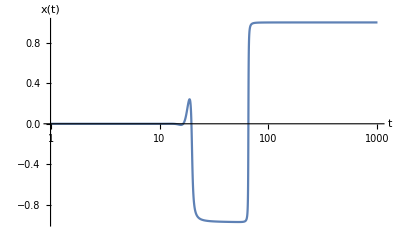

```mathematica
sol3=NDSolve[{r'[t]==r[t]*(1-r[t]^2)*(r[t]^2*Sin[v[t]]^2+(r[t]^2*Cos[v[t]]^2-1)^2),v'[t]==r[t]^2*Sin[v[t]]^2+(r[t]^2*Cos[v[t]]^2-1)^2,r[0]==0.000000001,v[0]==Pi/4},{r,v},{t,0,1000}];
Plot[Evaluate[r[t]*Cos[v[t]]/.sol3],{t,1,1000},PlotRange->All,AxesLabel->{t,x[t]},ScalingFunctions->{"Log",Automatic},PlotPoints->1000]
```

## Pregunta III

```mathematica
Solve[{x*(3-x-2*y)==0,y*(2-x-y)==0},{x,y}]
```

{{x→0,y→2},{x→1,y→1},{x→3,y→0},{x→0,y→0}}

```mathematica
j1={{D[x*(3-x-2*y),x],D[x*(3-x-2*y),y]},{D[y*(2-x-y),x],D[y*(2-x-y),y]}}
```

{{3-2 x-2 y,-2 x},{-y,2-x-2 y}}

```mathematica
MatrixForm[j1/.{x->0,y->0}]
```

(3 | 0
0 | 2)

```mathematica
MatrixForm[j1/.{x->3,y->0}]
```

(-3 | -6
0 | -1)

```mathematica
MatrixForm[j1/.{x->1,y->1}]
```

(-1 | -2
-1 | -1)

```mathematica
Eigensystem[j1/.{x->1,y->1}]
```

{{-1-√2,-1+√2},{{√2,1},{-√2,1}}}

```mathematica
MatrixForm[j1/.{x->0,y->2}]
```

(-1 | 0
-2 | -2)

```mathematica
sol4=NDSolve[{x'[t]==x[t]*(3-x[t]-2*y[t]),y'[t]==y[t]*(2-x[t]-y[t]),x[0]==0,y[0]==-0.00001},{x,y},{t,0,6}];
sol5=NDSolve[{x'[t]==x[t]*(3-x[t]-2*y[t]),y'[t]==y[t]*(2-x[t]-y[t]),x[4.6]==1+Sqrt[2]*0.00001,y[4.6]==1+0.00001},{x,y},{t,0,4.6}];
sol6=NDSolve[{x'[t]==x[t]*(3-x[t]-2*y[t]),y'[t]==y[t]*(2-x[t]-y[t]),x[10]==1-Sqrt[2]*0.00001,y[10]==1-0.00001},{x,y},{t,0,10}];
sol7=NDSolve[{x'[t]==x[t]*(3-x[t]-2*y[t]),y'[t]==y[t]*(2-x[t]-y[t]),x[0]==-0.00001,y[0]==0},{x,y},{t,0,4}];
```

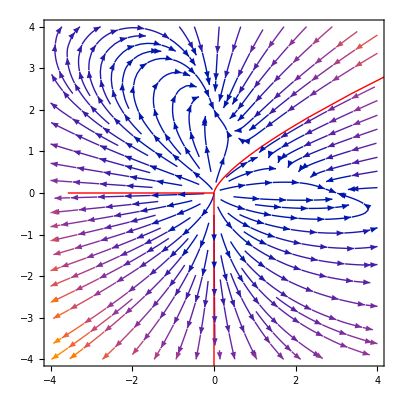

```mathematica
Show[{StreamPlot[{x*(3-x-2*y),y*(2-x-y)},{x,-4,4},{y,-4,4}],ParametricPlot[Evaluate[{x[t],y[t]}/.sol4],{t,0,6},PlotStyle->{Red,Thick}],ParametricPlot[Evaluate[{x[t],y[t]}/.sol5],{t,0,4.6},PlotStyle->{Red,Thick}],
ParametricPlot[Evaluate[{x[t],y[t]}/.sol6],{t,0,10},PlotStyle->{Red,Thick}],ParametricPlot[Evaluate[{x[t],y[t]}/.sol7],{t,0,4},PlotStyle->{Red,Thick}]}]
```

Las cuencas de atracción son las regiones inferior derecha y superior izquierda que rodean a cada nodo estable. Las soluciones en la región inferior izquierda, delimitada por los eigenvectores del nodo inestable, divergen.